# Introductory tutorial to Wolfram Mathematica

## References/Resources

1. This tutorial is to a great extent a transcript of this video .
2. The Wolfram Language and System Documentation Center (). Mathematica is very well documented and there are plenty of examples.

## Getting Started

You have a couple of options if you’d like to use Mathematica:

1. Mathematica is provided for free to UW students by UW College of Engineering. Before doing anything else, you should download and install Mathematica in your computer following the instructions under this link: . It works on Windows, OSX and Linux.

2. You can use the Wolfram Programming Lab to create Mathematica Notebooks online:

In this tutorial we’re mostly going to talk about the desktop Mathematica software, but you should be able to do everything on the online version as well. Once you have Mathematica installed in your computer, open it so that the welcome screen appears. From there, go to “New Document” and select “Notebook” from the drop down menu. This is the basic form of document produced by Mathematica, and it has the extension .nb. (As you can see, there are more options, like slideshows and presentations, but we won’t deal with those for now).

## Working with Cells/ Input Methods

Looking at the left of the notebook, you see some brackets that designate cells. A cell can be inside another one. Double clicking on a cell makes it contract, so that only its first line is visible. You can then see a little triangle at the bottom of the corresponding bracket, and you can double click on it again to expand it. 

There are three basic ways of inputting calculations:
1. Free form. This is essentially very similar as using Wolfram Alpha, and it requires an internet connection. You can type plain English in it, and it translates it into Wolfram language. You can initiate Free Form input by typing “=”. Then type your question and hit Shift+Enter.

WolframAlphaQueryResults

1.77245

2. Use Wolfram Language (this is probably the most efficient way of using Mathematica once you get used to it a little bit). There are four basic rules for typing in Wolfram Language:
	- Names of functions start with uppercase letter
	- Arguments of functions are enclosed by square brackets
	- Lists, ranges and domains are enclosed by curly braces
	- We use Shift+Enter to run calculations
Example:

```mathematica
Integrate[Exp[-t^2],{t,-Infinity,Infinity}]
```

√π

3. Use Palettes. Go to Palettes-> Basic Math assistant. There are many different operations you can perform using this palette. For example:

```mathematica
∫_(-∞)^∞ ⅇ^(-x^2)ⅆx
```

√π

## Computations

Mathematica performs exact computations whenever possible. For example:

```mathematica
172/56
```

43/14

If you want a numerical value you can use the function N:

```mathematica
N[172/56]
```

3.07143

You can prescribe arbitrary accuracy, say you want 40 digits:

```mathematica
N[172/56,40]
```

3.071428571428571428571428571428571428571

Another way to obtain numerical results in computations is to write

```mathematica
172./56
```

3.07143

In general, attaching an N in the beginning of certain commands performs them numerically. For example, NIntegrate stands for numerical integration:

```mathematica
NIntegrate[Exp[-t^2],{t,-Infinity,Infinity}]
```

```mathematica
1.7724538504129486
```

1.77245

You can also use variables

## Functions

The syntax for defining your own functions is the following (note that in this case you don’t necessarily have to use uppercase letters):

```mathematica
g[x_]:=x^2
```

We can differentiate our function:

```mathematica
g'[x]
```

2 x

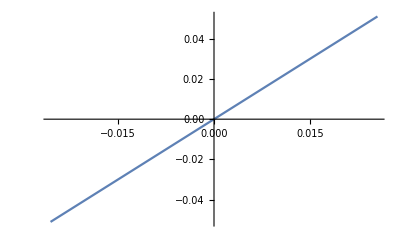

```mathematica
Plot[2 x,{x,-0.025500000000000002,0.025500000000000002}]
```

```mathematica
Solve[g[x]==8,x]
```

{{x→-2 √2},{x→2 √2}}

Again attaching an N before the Solve command solves the equation numerically

```mathematica
NSolve[g[x]==8,x]
```

```mathematica
{{x->-2.8284271247461903},{x->2.82842712474619}}
```

```mathematica
Limit[Sin[x]/x,x->0]
```

1

You can use Reduce to find roots of polynomials

```mathematica
Reduce[x^6 - x^4 - 4 x^2 + 4 == 0, x]
```

x==-1||x==1||x==-√2||x==-ⅈ √2||x==ⅈ √2||x==√2

## Basic Graphing

An example of plotting a function of a variable, you can play with the parameters as you please!

```mathematica
h[x_]:=x^2*Sin[x]
```

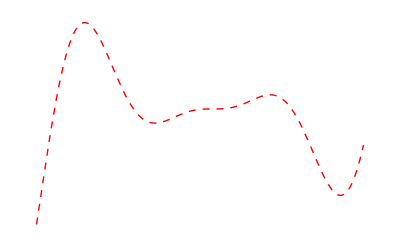

```mathematica
Plot[h[t],{t,-7,6},Axes->False,PlotStyle->{Thick,Red,Dashed}]
```

We can also plot functions of two variables:

```mathematica
Plot3D[Sin[x-y],{x,-4,2},{y,-6,8},Mesh->None,ClippingStyle->Red,PlotPoints->200]
```

-Graphics3D-

If you’d like to restrict the domain shown you can use RegionFunction:

```mathematica
Plot3D[Sin[x-y],{x,-4,2},{y,-6,8},Mesh->None,RegionFunction->Function[{x,y,z},.5≤x^2+y^2≤4],ClippingStyle->Red,PlotPoints->200,ViewPoint->{0, 0, 2}]
```

```mathematica
A=Plot3D[5-x^2,{x,0,2},{y,0,2},Mesh->None,RegionFunction->Function[{x,y,z},x^2+y^2≤1],PlotRange->{{0,1},{0,1},{0,5}}, ClippingStyle->Red,PlotPoints->200,ViewPoint->{5, 5, 5}]
```

-Graphics3D-

```mathematica
B=ParametricPlot3D[{√(1-y^2),y,z},{y,0,1},{z,0,5},RegionFunction->Function[{x,y,z},z≤5-x^2],ViewPoint->{5,5,5}]
```

-Graphics3D-

```mathematica
Show[A,B,ViewPoint->{5,5,5}]
```

-Graphics3D-

Table has a similar function to a for loop:

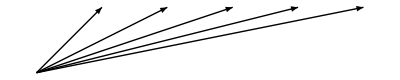

```mathematica
Graphics[Table[Arrow[{{0,0},{n,1}}],{n,1,5}]]
```

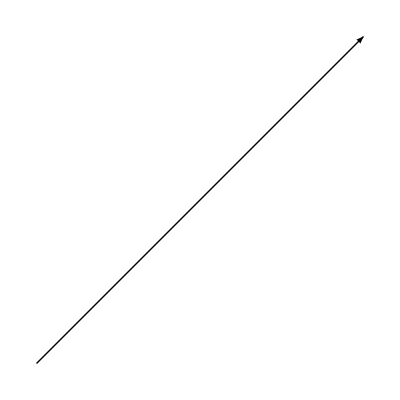
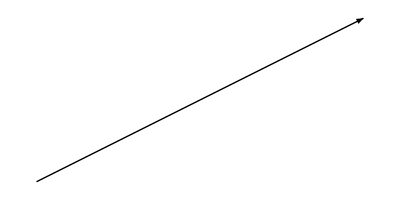
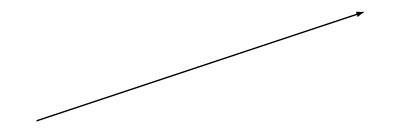
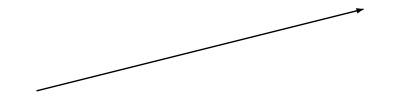
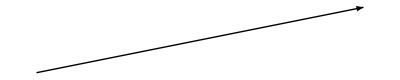

```mathematica
Table[Graphics[Arrow[{{0,0},{n,1}}]],{n,1,5}]
```

We can display a curve using parametric equations

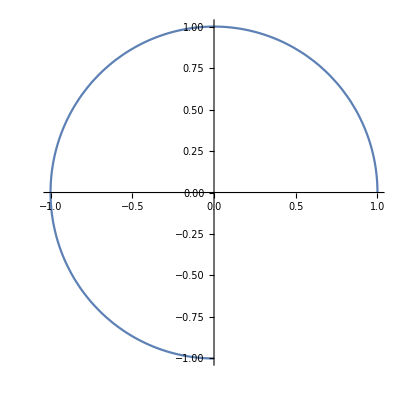

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,3Pi/2}]
```

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],t},{t,0,4Pi}]
```

-Graphics3D-

## Interactive Models

Let’s take the parametric plot and make it draw itself. We can use Animate:

```mathematica
Animate[ParametricPlot3D[{Cos[t],Sin[t],t},{t,0,s},PlotRange->{{-1,1},{-1,1},{0,4Pi}}],{s,0,4Pi},AnimationRunning->True]
```

```mathematica
Manipulate[Plot[Sin[k*t],{t,0,2Pi},PlotStyle->Color],{k,0,5},{Color,{Red,Black,Blue,Yellow}}]
```

## Some styling shortcuts

- To write π  without using a palette, hit Esc + p + Esc (this works for Greek letters in general)
- Instead of Sqrt[ ] you can hit Ctrl+2 to get √□.
- Instead of ^ you can hit Ctrl + 6 to get □^□.
- Instead of / you can hit Ctrl + / to get □/□.
In this context, Ctrl should work in all operating systems (that is, don’t replace it with Cmd if you’re using OSX).

## Remarks/Troubleshooting

- Unlike many other programming environments, Mathematica doesn’t auto-save whenever you run your code. So if you’re working on a large project make sure to save regularly. You can follow the instructions at  to turn on the auto-save option.
-  Notebooks running at the same time are not independent, in the sense that any value you assign to a variable in one notebook will be carried on to your other notebooks. So it might be a good idea to use the command Clear if you’re running multiple notebooks.

```mathematica
Clear[x]
```

- While a cell is evaluated, its bracket turns black. If the computation is taking too long you might want to abort it, by going to Evaluation-> Abort Evaluation.
- Sometimes Mathematica might be acting weird, and a way to restart it without terminating the program is to restart the kernel, by going to Evaluation -> Quit kernel